0.001

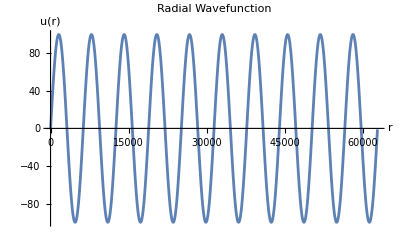

```mathematica
(*Constants*)
M=1;
m= 0.1*M(*0.1*M*); (*Hydrogen atom: m=0*)
α=1.1;
E0=m^2/(10*M)(*m^2/(10*M)*); (*Try different negative E for bound states*) (*Hydrogen atom: M=2m_e, E0=-M*α^2/(4n^2)*)
k=Sqrt[E0*M];
k=m/100
λ = 2*Pi/Abs[k]; (* De Broglie Wavelength*)

(*Potential*)
V[r_]:=-α*Exp[-m*r]/r;

(*Schrödinger equation*)
eq=u''[r]==(M*V[r]-k^2) u[r];

(*Boundary conditions*)
r0=10^-6;
bc={u[r0]==r0-α*M*r0^2/2,u'[r0]==1-α*M*r0}; (*r0 is a small value instead of r=0*)

(*Numerical solution*)
maxr = 10*λ; (*Graph much more than de broglie wavelength to ensure asmptotic behavior*)
sol=NDSolve[{eq,Sequence@@bc},u,{r,r0,maxr},MaxSteps->Infinity];

(*Plot the solution*)
Plot[Evaluate[u[r]/. sol],{r,r0,maxr},PlotRange->All,AxesLabel->{"r","u(r)"},PlotLabel->"Radial Wavefunction"]
```

```mathematica
Clear[δ]
fitRegion={r,0.8*maxr,maxr};
numericalData=Table[{r,u[r]/. sol[[1]]},{r,0.8*maxr,maxr,maxr/100}];

fitModel=NonlinearModelFit[numericalData,A*Sin[k*r+δ],{{A,1},{δ,0}},r];
fitModel["BestFitParameters"]
```

{A→99.774,δ→-0.0102493}